```mathematica
ClearAll["Global`*"]
```

```mathematica
(*G=6.67408*10^-11;*)
G=4Pi ^2;
tmax=400;
```

```mathematica
(* Mass *)
m=Flatten[Import[FileNameJoin[{NotebookDirectory[],  "mass.dat"}]]];
n=Length[m];
M=Sum[m[[i]],{i,n}];
```

```mathematica
(* Initial coord and vel *)
initCoords=Import[FileNameJoin[{NotebookDirectory[], "initpos.dat"}],"Table"];
initVels=Import[FileNameJoin[{NotebookDirectory[], "initvel.dat"}],"Table"];

R=Table[Sum[m[[i]] initCoords[[i,j]]/M,{i,n}],{j,3}];
Rdot=Table[Sum[m[[i]] initVels[[i,j]]/M,{i,n}],{j,3}];
```

```mathematica
(* Initial pos and mom relative to 1 *)
initpositions=Table[initpos[i][j],{i,n-1},{j,3}];
initmoments=Table[initmom[i][j],{i,n-1},{j,3}];

For[i=1,i≤n-1,i++,
For[j=1,j≤3,j++,
initpos[i][j]=initCoords[[1,j]]-initCoords[[i+1,j]];
initmom[i][j]=m[[i+1]](Rdot[[j]]-initVels[[i+1,j]])
]
]
Clear[i,j]
```

```mathematica
(* Defining position and moment variables *)
positions[t_]=Table[pos[i][j][t] ,{i,2,n},{j,3}];
moments[t_]=Table[mom[i][j][t] ,{i,2,n},{j,3}];

For[j=1,j≤3,j++,
pos[1][j][t]=0;
mom[1][j][t]=0
]
Clear[j]
```

```mathematica
(* Potential V *)
Normaij[posi__,i__,j_]:=Sqrt[Sum[(posi[[3( j-2)+k]]-posi[[3(i-2)+k]])^2,{k,3}]]
(*T[velo__]:=1/2(Sum[m[[i]]velo[[i]].velo[[i]],{i,n}])-1/2(Sum[m[[i]]m[[j]]/M velo[[i]].velo[[j]],{i,2,n},{j,2,n}]/M)*)
V[posi__]:=-G Sum[m[[1]]m[[i]]/Sqrt[Sum[posi[[3(i-2)+k]]^2,{k,3}]],{i,2,n}]-G Sum[If[i!=j,m[[i]]m[[j]]/(2*Normaij[posi,i,j]),0],{i,2,n},{j,2,n}]
```

```mathematica
(* Inverse Kinetic Matrix *)
Tmat=Table[If[i==j,m[[i]],0],{i,2,n},{j,2,n}]-Table[m[[i]]m[[j]]/M,{i,2,n},{j,2,n}];
Tmatinv = Inverse[Tmat];
Tmatinvext=Table[If[k==l,Tmatinv[[i,j]],0],{i,n-1},{k,3},{j,n-1},{l,3}];
Tinv = Map[Flatten,Flatten[Tmatinvext,1]];
```

```mathematica
(* Hamiltonean and variables *)
H[posi__,moment__]:=1/2*moment.Tinv.moment + V[posi]
hamiltoneq[1][i_,posi__,moment__,t_]:=( D[H[posi,moment],moment[[i]]]==D[posi[[i]],t])
hamiltoneq[2][i_,posi__,moment__,t_]:=( D[H[posi,moment],posi[[i]]]==-D[moment[[i]],t])

Vec[1][t_] := Flatten[positions[t]]
Vec[2][t_] := Flatten[moments[t]]
H[Vec[1][t],Vec[2][t]];
```

```mathematica
(*  *)
Hamiltoneqs[t_]= Flatten[Table[hamiltoneq[j][i,Vec[1][t],Vec[2][t],t],{j,2},{i,1,3*(n-1)}]];
initConditions=Table[If[j==1,initpos[i][k]==Vec[1][0][[3*(i-1)+k]],initmom[i][k]==Vec[2][0][[3*(i-1)+k]]],{j,2},{i,n-1},{k,3}];

equations[t_]:=Flatten[{Hamiltoneqs[t],initConditions}];
variables= Flatten[{Table[pos[i][j] ,{i,2,n},{j,3}],Table[mom[i][j] ,{i,2,n},{j,3}]}];
```

```mathematica
(* Solve ODEs *)
solution=Flatten[NDSolve[equations[t],variables,{t,0,tmax},MaxSteps->10000000,PrecisionGoal->30]];
```

```mathematica
(* Ref change to CM *)
For[i=2,i≤n,i++,
For[j=1,j≤3,j++,
pos[i][j] = pos[i][j]/.solution;
mom[i][j] = mom[i][j]/.solution
]
]
Clear[j]
```

```mathematica
CentreMass=Table[CM[i],{i,3}];
For[i=1,i≤3,i++,
CM[i][t_]=R[[i]]+Rdot[[i]] t
]
Clear[i]
```

```mathematica
InertialPositions=Table[inerpos[i][j],{i,n},{j,3}];
InertialMoments=Table[inermom[i][j],{i,n},{j,3}];

For[k=1,k≤3,k++,
inerpos[1][k][t_]=Sum[(m[[j]] pos[j][k][t])/M,{j,2,n}](*+CM[k][t]*);
inermom[1][k][t_]=Sum[mom[i][k][t],{i,2,n}]
]
For[i=2,i≤n,i++,
For[j=1,j≤3,j++,
inerpos[i][j][t_]=inerpos[1][j][t]-pos[i][j][t](*+CM[j][t]*);
inermom[i][j][t_]=-mom[i][j][t]
]
]
Clear[i,k,j]
```

```mathematica
(* Plots *)
ParametricPlot3D[Evaluate[Table[inerpos[i][j][t],{i,n}, {j,3}]],{t,0,tmax},PlotRange->All,AspectRatio->1]
```

-Graphics3D-

```mathematica
DumpGet["temp1.mx"]
```

```mathematica
ParametricPlot3D[Evaluate[Table[pos[4][j][t]-pos1[2][j][t],{j,3}]],{t,0,tmax},PlotRange->All,AspectRatio->1];
```

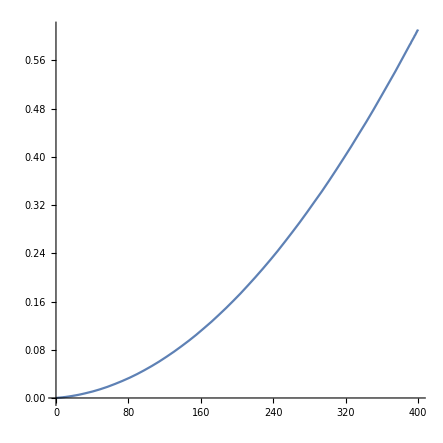

```mathematica
Plot[Evaluate[Sqrt[Sum[(pos[4][j][t]-pos1[2][j][t])^2,{j,3}]]],{t,0,tmax},PlotRange->All,AspectRatio->1]
```

```mathematica
(*FindMinimum[Sqrt[Sum[(pos[4][j][t]-pos1[2][j][t])^2,{j,3}]],{t,3000}]
FindMinimum[Sqrt[Sum[(pos[4][j][t]-pos1[2][j][t])^2,{j,3}]],{t,3200}]
FindMinimum[Sqrt[Sum[(pos[4][j][t]-pos1[2][j][t])^2,{j,3}]],{t,3500}]
FindMinimum[Sqrt[Sum[(pos[4][j][t]-pos1[2][j][t])^2,{j,3}]],{t,3800}]
FindMinimum[Sqrt[Sum[(pos[4][j][t]-pos1[2][j][t])^2,{j,3}]],{t,4000}]*)
```

```mathematica
3257-2970
```

287

```mathematica
3522-3257
```

265

```mathematica
3769-3522
```

247

```mathematica
4000.08-3769
```

231.08

```mathematica
N[1/231]
```

0.004329

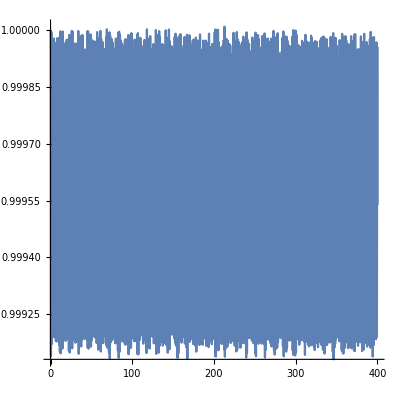

```mathematica
Plot[Evaluate[Sqrt[Sum[(pos[4][j][t])^2,{j,3}]]],{t,0,tmax},PlotRange->All,AspectRatio->1]
```

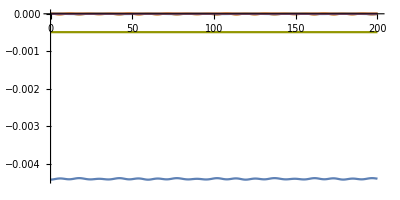

```mathematica
(* Energies for each body and Total *)
Kinetic[t_]=Table[Sum[inermom[i][j][t]^2,{j,3}]/(2 m[[i]]),{i,n}];
Potential[t_]=Table[-G Sum[If[i≠k,m[[i]]m[[k]]/(2Sqrt[Sum[(inerpos[i][j][t]-inerpos[k][j][t])^2,{j,3}]]),0],{k,n}],{i,n}];
Energy[t_]=Table[{t,Kinetic[t][[i]]+Potential[t][[i]]},{i,n}];
TotalEnergy[t_]={{t,Sum[Energy[t][[i,2]],{i,n}]/n}};
ParametricPlot[Evaluate[Join[Energy[t],TotalEnergy[t]]],{t,0,200},PlotRange->All, AspectRatio->0.5]
```

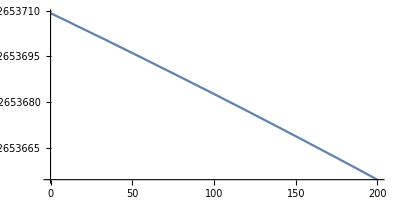

```mathematica
(* Momentum for each body and Total *)
AngMomentum[t_]=Table[Cross[Table[inerpos[i][j][t],{j,3}],Table[inermom[i][j][t],{j,3}]],{i,n}];
TotalAngMom[t_]=Sum[AngMomentum[t][[i]],{i,n}];

ParametricPlot[Evaluate[{t,Norm[TotalAngMom[t]]}],{t,0,200},PlotRange->All,AspectRatio->0.5]
```